```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc

# Fluc data

```mathematica
r42low=Import["./phasedata_v2/r42low.dat"];
r42high=Import["./phasedata_v3/r42high.dat"];
r42high2=Import["./phasedata_v4/r42high2.dat"];
r42high3=Import["./phasedata_v5/r42high3.dat"];
```

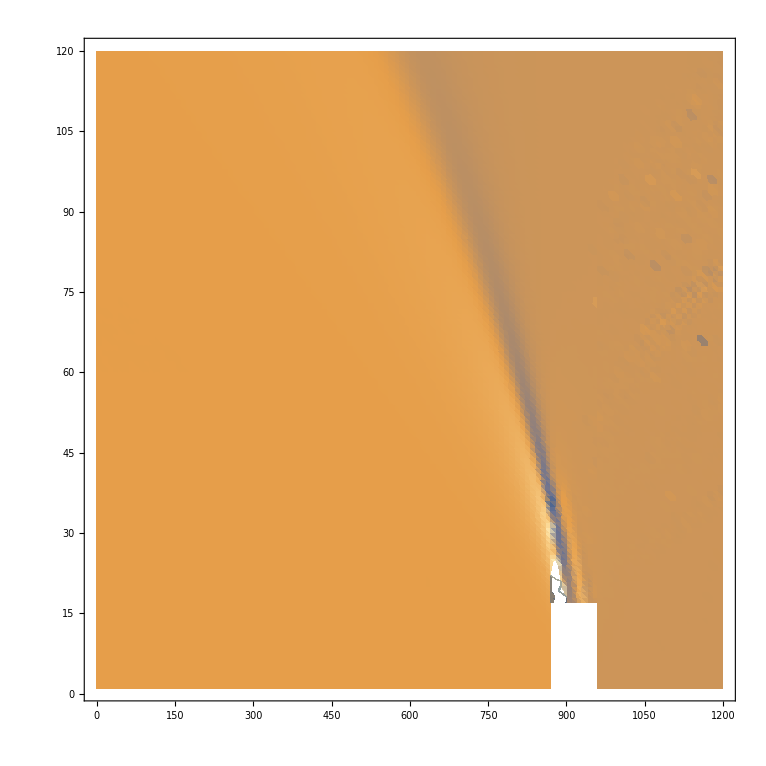

```mathematica
ListDensityPlot[{r42low,r42high,r42high3},PlotRange->{All,All,{-7,9}}]
```

# Freeze-out

```mathematica
a=1307.5;
b=0.288;
c=2.6;
d=0.45;
```

```mathematica
Clear[a,b,c,d]
```

```mathematica
Solve[mub==a/(1+b sqrts),{sqrts}]
```

{{sqrts→(a-mub)/(b mub)}}

```mathematica
Tcf/(1+Exp[c-Log[sqrts]/d])/.{sqrts->(a-mub)/(b mub)}
```

Tcf/(1+ⅇ^(c-Log[(a-mub)/(b mub)]/d))

```mathematica
T1[mub_,Tcf_,a_,b_,c_,d_]:=Tcf/(1+ⅇ^(c-Log[(a-mub)/(b mub)]/d));
```

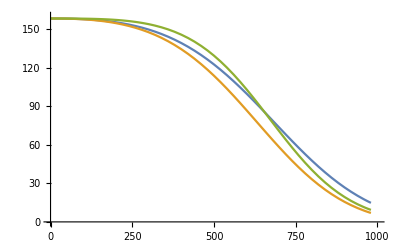

```mathematica
Plot[{T1[x,158.4,1307.5,0.288,2.6,0.45],T1[x,158.4,1207.5,0.288,2.6,0.45],T1[x,158.4,1357.5,0.288,3.6,0.35]},{x,0,980},PlotRange->{{0,1000},{0,160}}]
```